```mathematica
Bldata=Import["~/Desktop/Tensor/Tensor learning/toy_model/Bl.txt","Table"]
```

{{0.197012,1.0092,0.125287,0.579831,-0.113549,0.392633,0.0274101,0.602658},{0.40976,0.741716,0.846437,-0.32684,-0.00355781,0.254346,0.400245,0.133909},{0.352273,0.853602,0.819046,-0.273528,-0.281323,0.794959,0.267896,0.3915},{0.443724,0.63639,0.987322,-0.673217,-0.207254,0.619033,0.404188,0.0677804},{0.442215,0.69757,0.987046,-0.662023,-0.213957,0.890767,0.402961,0.117501},{0.402511,0.815637,0.906011,-0.42105,-0.215462,0.895242,0.39989,0.126633},{0.251657,0.853023,0.794666,-0.393456,-0.528517,0.972826,0.168826,0.183898},{0.394353,0.700622,1.05698,-0.673605,-0.445267,0.883914,0.321859,0.0204572},{0.405491,0.712119,1.06037,-0.670101,-0.419858,0.910143,0.329603,0.0284513},{0.377244,0.781721,0.969788,-0.4469,-0.433252,0.943146,0.286652,0.134287},{0.416631,0.761078,0.98124,-0.452902,-0.294949,0.870663,0.326866,0.113211},{0.384414,0.722781,0.924305,-0.520585,-0.301055,0.863406,0.316076,0.100384},{0.395785,0.709742,0.926246,-0.522811,-0.272066,0.830165,0.321025,0.0947096},{0.403956,0.657668,0.939286,-0.605914,-0.269316,0.812643,0.325413,0.066746},{0.399035,0.688223,0.937346,-0.59387,-0.29194,0.953099,0.316495,0.122111},{0.397147,0.728872,0.931369,-0.46513,-0.292844,0.97256,0.313633,0.183748},{0.30615,0.686054,0.895385,-0.482062,-0.459184,0.89429,0.247856,0.152797},{0.419507,0.593516,1.12464,-0.66921,-0.299052,0.763566,0.571705,-0.111577},{0.373329,0.666569,1.1082,-0.643203,-0.439051,0.985044,0.521866,-0.0327314},{0.362767,0.676794,1.07794,-0.613916,-0.450547,0.996173,0.488939,-0.000853994}}

```mathematica
tf1={Cos[x],Sin[x]}
```

{Cos[x],Sin[x]}

```mathematica
tf2={Cos[y],Sin[y]}
```

{Cos[y],Sin[y]}

```mathematica
Am =  {{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
A = {{0},{0}}
```

{{0},{0}}

```mathematica
For[n=1,n≤1,n++,
Bl=Table[Bldata[[n,(i1-1)*4+(i2-1)*2+ (i3-1)+1]],{i1,2},{i2,2},{i3,2}];
Am = {{0,0},{0,0}};
For[i=1,i≤2,i++,Am+=tf1[[i]]*Bl[[i,All]]];
A = {{0},{0}};
For[j=1,j≤2,j++,A+=tf2[[j]]*Am[[j,All]]];
ContourPlot[A[[1,1]]==A[[2,1]],{x,-2,2},{y,-2,2}]
]
```

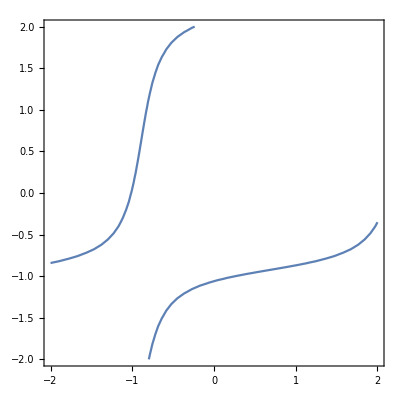
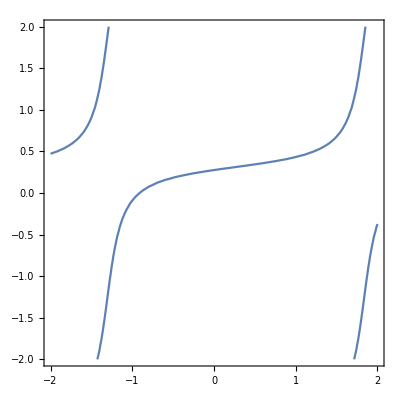
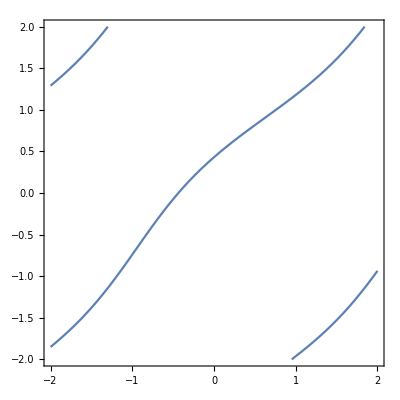
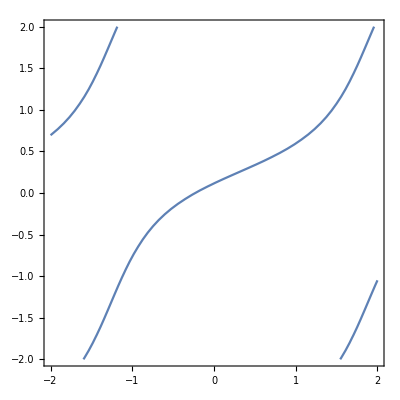
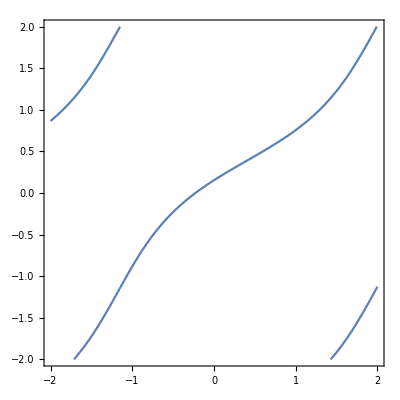
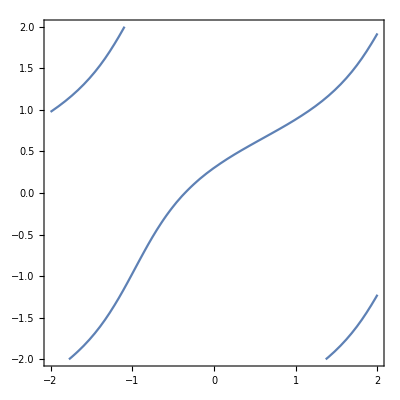
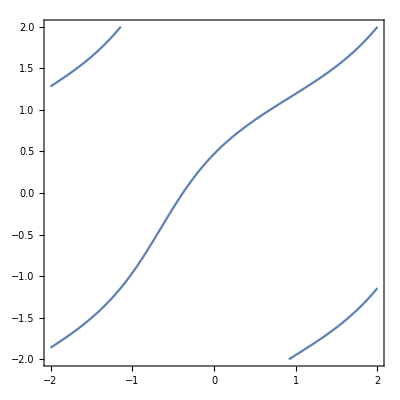
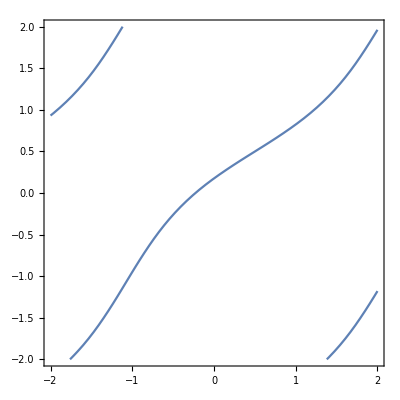

```mathematica
Table[Bl=Table[Bldata[[n,(i1-1)*4+(i2-1)*2+ (i3-1)+1]],{i1,2},{i2,2},{i3,2}];
Am = {{0,0},{0,0}};
For[i=1,i≤2,i++,Am+=tf1[[i]]*Bl[[i,All]]];
A = {{0},{0}};
For[j=1,j≤2,j++,A+=tf2[[j]]*Am[[j,All]]];
ContourPlot[A[[1,1]]==A[[2,1]],{x,-2,2},{y,-2,2}],{n,1,10}
]
```

```mathematica
linelist = {}
```

{}

```mathematica
For[n=1,n≤1,n++,
Bl=Table[Bldata[[n,(i1-1)*4+(i2-1)*2+ (i3-1)+1]],{i1,2},{i2,2},{i3,2}];
Am = {{0,0},{0,0}};
For[i=1,i≤2,i++,Am+=tf1[[i]]*Bl[[i,All]]];
A = {{0},{0}};
For[j=1,j≤2,j++,A+=tf2[[j]]*Am[[j,All]]];
AppendTo[linelist,A]
]
```

```mathematica
linelist
```

{{{Cos[y] (0.197012 Cos[x]-0.113549 Sin[x])+(0.125287 Cos[x]+0.0274101 Sin[x]) Sin[y]},{Cos[y] (1.0092 Cos[x]+0.392633 Sin[x])+(0.579831 Cos[x]+0.602658 Sin[x]) Sin[y]}}}

```mathematica
Blist = Table[Bl=Table[Bldata[[n,(i1-1)*4+(i2-1)*2+ (i3-1)+1]],{i1,2},{i2,2},{i3,2}],{n,1,10}
]
```

{{{{0.197012,1.0092},{0.125287,0.579831}},{{-0.113549,0.392633},{0.0274101,0.602658}}},{{{0.40976,0.741716},{0.846437,-0.32684}},{{-0.00355781,0.254346},{0.400245,0.133909}}},{{{0.352273,0.853602},{0.819046,-0.273528}},{{-0.281323,0.794959},{0.267896,0.3915}}},{{{0.443724,0.63639},{0.987322,-0.673217}},{{-0.207254,0.619033},{0.404188,0.0677804}}},{{{0.442215,0.69757},{0.987046,-0.662023}},{{-0.213957,0.890767},{0.402961,0.117501}}},{{{0.402511,0.815637},{0.906011,-0.42105}},{{-0.215462,0.895242},{0.39989,0.126633}}},{{{0.251657,0.853023},{0.794666,-0.393456}},{{-0.528517,0.972826},{0.168826,0.183898}}},{{{0.394353,0.700622},{1.05698,-0.673605}},{{-0.445267,0.883914},{0.321859,0.0204572}}},{{{0.405491,0.712119},{1.06037,-0.670101}},{{-0.419858,0.910143},{0.329603,0.0284513}}},{{{0.377244,0.781721},{0.969788,-0.4469}},{{-0.433252,0.943146},{0.286652,0.134287}}}}

```mathematica
Alist = Table[Bl=Table[Bldata[[n,(i1-1)*4+(i2-1)*2+ (i3-1)+1]],{i1,2},{i2,2},{i3,2}];
Am = {{0,0},{0,0}};
For[i=1,i≤2,i++,Am+=tf1[[i]]*Bl[[i,All]]];
A = {{0},{0}};
For[j=1,j≤2,j++,A+=tf2[[j]]*Am[[j,All]]];
A,{n,1,10}
]
```

{{{Cos[y] (0.197012 Cos[x]-0.113549 Sin[x])+(0.125287 Cos[x]+0.0274101 Sin[x]) Sin[y]},{Cos[y] (1.0092 Cos[x]+0.392633 Sin[x])+(0.579831 Cos[x]+0.602658 Sin[x]) Sin[y]}},{{Cos[y] (0.40976 Cos[x]-0.00355781 Sin[x])+(0.846437 Cos[x]+0.400245 Sin[x]) Sin[y]},{Cos[y] (0.741716 Cos[x]+0.254346 Sin[x])+(-0.32684 Cos[x]+0.133909 Sin[x]) Sin[y]}},{{Cos[y] (0.352273 Cos[x]-0.281323 Sin[x])+(0.819046 Cos[x]+0.267896 Sin[x]) Sin[y]},{Cos[y] (0.853602 Cos[x]+0.794959 Sin[x])+(-0.273528 Cos[x]+0.3915 Sin[x]) Sin[y]}},{{Cos[y] (0.443724 Cos[x]-0.207254 Sin[x])+(0.987322 Cos[x]+0.404188 Sin[x]) Sin[y]},{Cos[y] (0.63639 Cos[x]+0.619033 Sin[x])+(-0.673217 Cos[x]+0.0677804 Sin[x]) Sin[y]}},{{Cos[y] (0.442215 Cos[x]-0.213957 Sin[x])+(0.987046 Cos[x]+0.402961 Sin[x]) Sin[y]},{Cos[y] (0.69757 Cos[x]+0.890767 Sin[x])+(-0.662023 Cos[x]+0.117501 Sin[x]) Sin[y]}},{{Cos[y] (0.402511 Cos[x]-0.215462 Sin[x])+(0.906011 Cos[x]+0.39989 Sin[x]) Sin[y]},{Cos[y] (0.815637 Cos[x]+0.895242 Sin[x])+(-0.42105 Cos[x]+0.126633 Sin[x]) Sin[y]}},{{Cos[y] (0.251657 Cos[x]-0.528517 Sin[x])+(0.794666 Cos[x]+0.168826 Sin[x]) Sin[y]},{Cos[y] (0.853023 Cos[x]+0.972826 Sin[x])+(-0.393456 Cos[x]+0.183898 Sin[x]) Sin[y]}},{{Cos[y] (0.394353 Cos[x]-0.445267 Sin[x])+(1.05698 Cos[x]+0.321859 Sin[x]) Sin[y]},{Cos[y] (0.700622 Cos[x]+0.883914 Sin[x])+(-0.673605 Cos[x]+0.0204572 Sin[x]) Sin[y]}},{{Cos[y] (0.405491 Cos[x]-0.419858 Sin[x])+(1.06037 Cos[x]+0.329603 Sin[x]) Sin[y]},{Cos[y] (0.712119 Cos[x]+0.910143 Sin[x])+(-0.670101 Cos[x]+0.0284513 Sin[x]) Sin[y]}},{{Cos[y] (0.377244 Cos[x]-0.433252 Sin[x])+(0.969788 Cos[x]+0.286652 Sin[x]) Sin[y]},{Cos[y] (0.781721 Cos[x]+0.943146 Sin[x])+(-0.4469 Cos[x]+0.134287 Sin[x]) Sin[y]}}}

```mathematica
Alist[[10,2]]
```

{Cos[y] (0.781721 Cos[x]+0.943146 Sin[x])+(-0.4469 Cos[x]+0.134287 Sin[x]) Sin[y]}

```mathematica
ListAnimate[Table[ContourPlot[Alist[[n,1]]==Alist[[n,2]],{x,-2,2},{y,-2,2}],{n,10}]]
```

```mathematica
ContourPlot[Alist[[2,1]]==Alist[[2,2]],{x,-2,2},{y,-2,2}]
```

-Graphics-